```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
U[G_]:=G^2/12;
a=1/(√6);
W=k (E^(a ϕ[z])(U[G[z]]+1-a ϕ[z])-1);
Vt=18(D[W,ϕ[z]]^2+D[W,G[z]]^2)-12 W^2-24k(0) W//FullSimplify
(*Vt=Exp[2a ϕ[z]](-12(1-E^(-2a ϕ[z]))+4 √6 ϕ[z]-3/2 ϕ[z]^2+3 √6 ϕ[z]U[G[z]]-24U[G[z]]-9 U[G[z]]^2+18(U'[G[z]])^2)k^2//FullSimplify*)
eqnϕ=36(D[W,{ϕ[z],1}]D[W,{ϕ[z],2}]+D[W,{G[z],1}]D[W,{ϕ[z],1},{G[z],1}])-24(W+k)D[W,{ϕ[z],1}]==D[Vt,ϕ[z]]//FullSimplify;
Print[StringForm["eqn(ϕ)==``",eqnϕ]];
eqnG=36(D[W,{ϕ[z],1}]D[W,{ϕ[z],1},{G[z],1}]+D[W,{G[z],1}]D[W,{G[z],2}])-24(W+k)D[W,{G[z],1}]==D[Vt,G[z]]//FullSimplify;
Print[StringForm["eqn(G)==``",eqnG]];
Print[StringForm["eqn(B')==``",True]];
eqnW=18(D[W+0k,ϕ[z]]^2+D[W+0k,G[z]]^2)-12(W+0k)^2==Vt-12 k^2//FullSimplify;
Print[StringForm["eqn(W)==``",eqnW]];
```

1/48 k^2 (-576 (1-1/12 ⅇ^(ϕ[z]/(√6)) (12+G[z]^2-2 √6 ϕ[z]))^2+ⅇ^(√(2/3) ϕ[z]) (G[z]^4+24 ϕ[z]^2-4 G[z]^2 (-6+√6 ϕ[z])))

eqn(ϕ)==ⅇ^ϕ[z]/√6\ k\ (-√6\ G[z]^2 + 12\ ϕ[z]) == 0

eqn(G)==ⅇ^ϕ[z]/√6\ k\ G[z] == 0

eqn(B')==True

eqn(W)==k == 0

```mathematica
z[y_]:=(-1+ⅇ^(k ∫_0^y ⅇ^(a ϕ[yp])ⅆyp))/k;
(*ϕ[z_]:=√(8/3)λ(z+1/k)^2;
G[z_]:=√((36ϕ[z])/(√6));*)
FullSimplify[Series[ϕ[z[ϵ]],{ϵ,0,1}]//Normal,Assumptions->λ>0&&k>0]
FullSimplify[Series[G[z[ϵ]],{ϵ,0,1}]//Normal,Assumptions->λ>0&&k>0]
FullSimplify[Series[D[ϕ[z[y]],y]/.y->ϵ,{ϵ,0,1}]//Normal,Assumptions->λ>0&&k>0]
FullSimplify[Series[D[G[z[y]],y]/.y->ϵ,{ϵ,0,1}]//Normal,Assumptions->λ>0&&k>0]
Table[(D[ϕ[y],{y,n}]/.y->0)->(D[√(8/3)λ(z+1/k)^2,{z,n}]/.z->0),{n,0,2}]
Table[(D[G[y],{y,n}]/.y->0)->(D[√(24λ)(z+1/k),{z,n}]/.z->0),{n,0,2}]
```

ϕ[0]+ⅇ^(a ϕ[0]) ϵ ϕ'[0]

G[0]+ⅇ^(a ϕ[0]) ϵ G'[0]

ⅇ^(a ϕ[0]) ϕ'[0] (1+a ϵ ϕ'[0])+ⅇ^(2 a ϕ[0]) ϵ (k ϕ'[0]+ϕ''[0])

ⅇ^(a ϕ[0]) G'[0] (1+a ϵ ϕ'[0])+ⅇ^(2 a ϕ[0]) ϵ (k G'[0]+G''[0])

{ϕ[0]→(2 √(2/3) λ)/k^2,ϕ'[0]→(4 √(2/3) λ)/k,ϕ''[0]→4 √(2/3) λ}

{G[0]→(2 √6 √λ)/k,G'[0]→2 √6 √λ,G''[0]→0}

```mathematica
B0=0;f0=1;fp0=0;a=1/√6;
FullSimplify[ϕ0=Sqrt[8/3] λ (z+1/k)^2/.z->0,Reals&&k>0];
FullSimplify[G0=Sqrt[36ϕ0/Sqrt[6]],Reals&&k>0];
FullSimplify[ϕp0=D[Sqrt[8/3] λ (z+1/k)^2,z]//.{z->0,ϕ0f[0]->ϕ0,ϕ0f'[0]->ϕp0},Reals&&k>0];
FullSimplify[Gp0=(D[Sqrt[36ϕ0f[z]/Sqrt[6]],z])//.{z->0,ϕ0f[0]->ϕ0,ϕ0f'[0]->ϕp0},Reals&&k>0];
Bp0=Exp[2a ϕ[0]] 1/6(ϕp0^2+Gp0^2)//.{z->0,ϕ[0]->ϕ0,G[0]->G0}
Vt-12 k^2//.{z->0,ϕ[0]->ϕ0,G[0]->G0}//FullSimplify
3(f0 Bp0+fp0 (B0+0k))-12f0(B0+0k)^2//.{z->0,ϕ[0]->ϕ0,G[0]->G0}//FullSimplify
3(f0 Bp0+fp0 (B0+0k))-12f0(B0+0k)^2==Vt-12 k^2//.{z->0,ϕ[0]->ϕ0,G[0]->G0}//FullSimplify
```

```mathematica
FullSimplify[ϕϵ=Sqrt[8/3] λ (z+1/k)^2/.z->ϵ,Reals&&k>0&&ϵ>0]
FullSimplify[Gϵ=Sqrt[ϕϵ/Sqrt[6] 36],Reals&&k>0&&ϵ>0]
FullSimplify[ϕpϵ=D[Sqrt[8/3] λ (z+1/k)^2,z]//.{z->ϵ,ϕ0f[ϵ]->ϕϵ,ϕ0f'[ϵ]->ϕpϵ},Reals&&k>0&&ϵ>0]
FullSimplify[Gpϵ=(D[Sqrt[ϕ0f[z]/Sqrt[6] 36],z])//.{z->ϵ,ϕ0f[ϵ]->ϕϵ,ϕ0f'[ϵ]->ϕpϵ},Reals&&k>0&&ϵ>0]
```

(2 √(2/3) λ)/k^2

(2 √6 √λ)/k

(4 √(2/3) λ)/k

2 √6 √λ

2 √(2/3) (1/k+ϵ)^2 λ

2 √6 (1/k+ϵ) √λ

4 √(2/3) (1/k+ϵ) λ

2 √6 √λ

```mathematica
Series[Exp[-a ϕ[z]],{z,0,1}]//FullSimplify
Series[Exp[-a ϕ[z]]/(k z+1),{z,0,1}]//FullSimplify
```

ⅇ^(-a ϕ[0])-a ⅇ^(-a ϕ[0]) ϕ'[0] z+O[z]^2

ⅇ^(-a ϕ[0])-ⅇ^(-a ϕ[0]) (k+a ϕ'[0]) z+O[z]^2

```mathematica
DSolve[(z+k^-1) G'[z]==6 D[G[z]^2/12,G[z]],G[z],z]
DSolve[(z+k^-1) ϕ'[z]+ϕ[z]==Sqrt[6] G[z]^2/12/.%[[1]],ϕ[z],z]/.C[2]->0//FullSimplify
Solve[(((1+k z)^2 C[1]^2)/(6 √6)/.z->0)==√(8/3)λ/k^2,C[1]]
```

{{G[z]→(1+k z) C[1]}}

{{ϕ[z]→((1+k z)^2 C[1]^2)/(6 √6)}}

{{C[1]→-(2 √6 √λ)/k},{C[1]→(2 √6 √λ)/k}}

```mathematica
Solve[3f Bp+3 fp(B+q)-12 f(B+q)^2==Vt-12 k^2,fp]//FullSimplify
Solve[f ψp+fp ψ-4f(B+q)ψ==dVtdϕ/.{fp->(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))},ψp]//FullSimplify
Solve[f γp+fp γ-4f(B+q)γ==dVtdG/.{fp->(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))},γp]//FullSimplify
```

{{fp→(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))}}

{{ψp→(3 dVtdϕ+((3 Bp f+12 k^2-Vt) ψ)/(B+q))/(3 f)}}

{{γp→(3 dVtdG+((3 Bp f+12 k^2-Vt) γ)/(B+q))/(3 f)}}

```mathematica
D[(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))/.Bp->1/6(ψ^2+γ^2),B]//FullSimplify
D[(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))/.Bp->1/6(ψ^2+γ^2),f]//FullSimplify
D[(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))/.Bp->1/6(ψ^2+γ^2),ψ]//FullSimplify
D[(-12 k^2+3 f (-Bp+4 (B+q)^2)+Vt)/(3 (B+q))/.Bp->1/6(ψ^2+γ^2),γ]//FullSimplify
```

(24 k^2-2 Vt+f (24 (B+q)^2+γ^2+ψ^2))/(6 (B+q)^2)

-(-4 (B+q)^2+1/6 (γ^2+ψ^2))/(B+q)

-(f ψ)/(3 (B+q))

-(f γ)/(3 (B+q))

```mathematica
D[(3 dVtdϕ+((3 Bp f+12 k^2-Vt) ψ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),B]//FullSimplify
D[(3 dVtdϕ+((3 Bp f+12 k^2-Vt) ψ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),f]//FullSimplify
D[(3 dVtdϕ+((3 Bp f+12 k^2-Vt) ψ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),ψ]//FullSimplify
D[(3 dVtdϕ+((3 Bp f+12 k^2-Vt) ψ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),γ]//FullSimplify
```

-(ψ (24 k^2-2 Vt+f (γ^2+ψ^2)))/(6 f (B+q)^2)

(-3 dVtdϕ (B+q)+(-12 k^2+Vt) ψ)/(3 f^2 (B+q))

(24 k^2-2 Vt+f γ^2+3 f ψ^2)/(6 B f+6 f q)

(γ ψ)/(3 (B+q))

```mathematica
D[(3 dVtdG+((3 Bp f+12 k^2-Vt) γ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),B]//FullSimplify
D[(3 dVtdG+((3 Bp f+12 k^2-Vt) γ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),f]//FullSimplify
D[(3 dVtdG+((3 Bp f+12 k^2-Vt) γ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),ψ]//FullSimplify
D[(3 dVtdG+((3 Bp f+12 k^2-Vt) γ)/(B+q))/(3 f)/.Bp->1/6(ψ^2+γ^2),γ]//FullSimplify
```

-(γ (24 k^2-2 Vt+f (γ^2+ψ^2)))/(6 f (B+q)^2)

(-3 dVtdG (B+q)+(-12 k^2+Vt) γ)/(3 f^2 (B+q))

(γ ψ)/(3 (B+q))

(24 k^2-2 Vt+3 f γ^2+f ψ^2)/(6 B f+6 f q)

```mathematica
DSolve[{3D[f[y]Bt[y],y]-12f[y] Bt[y]^2==Vt[y]-12 k^2,f[0]==1},f[y],y]//FullSimplify
```

{{f[y]→ⅇ^(∫_1^y (4 Bt[K[1]]-Bt'[K[1]]/Bt[K[1]])ⅆK[1]) (ⅇ^(-∫_1^0 (4 Bt[K[1]]-Bt'[K[1]]/Bt[K[1]])ⅆK[1])-∫_1^0 (ⅇ^(-∫_1^K[2] (4 Bt[K[1]]-Bt'[K[1]]/Bt[K[1]])ⅆK[1]) (-12 k^2+Vt[K[2]]))/(3 Bt[K[2]])ⅆK[2]+∫_1^y (ⅇ^(-∫_1^K[2] (4 Bt[K[1]]-Bt'[K[1]]/Bt[K[1]])ⅆK[1]) (-12 k^2+Vt[K[2]]))/(3 Bt[K[2]])ⅆK[2])}}

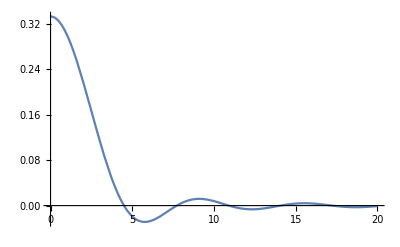

```mathematica
Plot[(Sin[z]-z Cos[z])/z^3,{z,0,20},PlotRange->All]
```

```mathematica
(Sin[z]-z Cos[z])/z^3//FullSimplify
```

(-z Cos[z]+Sin[z])/z^3

```mathematica
SphericalBesselJ[2,z]-3 SphericalBesselJ[1,z]/z==-SphericalBesselJ[0,z]//FullSimplify
```

True

```mathematica
FourierTransform[Exp[-I ω x]/x,x,k]
```

ⅈ √(π/2) Sign[k-ω]